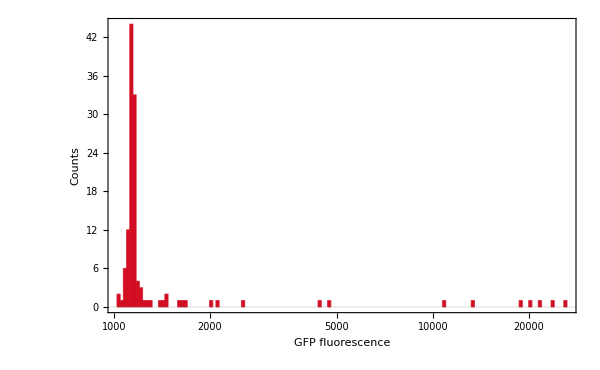

```mathematica
$PlotTheme = "Scientific";
fileName = "redstate014RFP.txt";
myGreen = RGBColor[25/255,188/255,157/255];
myRed = RGBColor[210/255,13/255,34/255];

data=Import[FileNameJoin[{NotebookDirectory[],"redState",fileName}],"Table"][[1;;-2,3]];
histoPlot=Histogram[data, {"Log",100}, ChartBaseStyle->myRed,FrameLabel->{"GFP fluorescence","Counts"}, LabelStyle->Medium,ImageSize->600]
```

```mathematica
Export[NotebookDirectory[]<>"histo_"<>FileBaseName@fileName<>".pdf", histoPlot]
```

C:\Users\Simon\Desktop\Genetic-Toggle-Switch-Lab\Part03\forSimon\histo_redstate014RFP.pdf